```mathematica
MaximizeQ[elem_,θ_]:=Module[{m,pos},
pos=Position[elem,_Symbol];
If[MemberQ[Extract[elem, pos], θ],
m=Maximize[elem,θ];
{m[[1]],θ/.m[[2]]},
{Max[elem],0}
]
];
MinimizeQ[elem_,θ_]:=Module[{m,pos},
pos=Position[elem,_Symbol];
If[MemberQ[Extract[elem, pos], θ],
m=Minimize[elem,θ];
{m[[1]],θ/.m[[2]]},
{Min[elem],0}
]
];
```

```mathematica
boxMax[M_]:=Module[{m,val,angle},
{Max[M[[1]]],Max[M[[2]]],Max[M[[3]]]}
]
boxMax[M_,θ_]:=Module[{pos,m,val,angle},
m={Map[MaximizeQ[#,θ]&,M[[1]]],Map[MaximizeQ[#,θ]&,M[[2]]],Map[MaximizeQ[#,θ]&,M[[3]]]};
val = m[[All,All,1]];
angle = m[[All,All,2]];
pos =Map[Ordering[#]&,val][[All,-1]];
{MapThread[Part[#1,#2]&,{val,pos}],MapThread[Part[#1,#2]&,{angle,pos}]}
]
boxMin[M_]:=Module[{m,val,angle},
{ Min[M[[1]]], Min[M[[2]]], Min[M[[3]]]}
]
boxMin[M_,θ_]:=Module[{pos,m,val,angle},
m={Map[ MinimizeQ[#,θ]&,M[[1]]],Map[ MinimizeQ[#,θ]&,M[[2]]],Map[ MinimizeQ[#,θ]&,M[[3]]]};
val = m[[All,All,1]];
angle = m[[All,All,2]];
pos =Map[Ordering[#]&,val][[All,1]];
{MapThread[Part[#1,#2]&,{val,pos}],MapThread[Part[#1,#2]&,{angle,pos}]}
]
boxRange[M_]:=Module[{m,val,angle},
Transpose[{boxMin[M],boxMax[M]}]
]
boxRange[M_,θ_]:=Module[{minVal,minAng, maxVal,maxAng},
{minVal,minAng}=boxMin[M,θ];
{maxVal,maxAng}=boxMax[M,θ];
{Transpose[{minVal,maxVal}],Transpose[{minAng,maxAng}]}
]
```

```mathematica
A[Kr_:0.299,Kb_:0.114]:={{Kr  ,(1+(-1) Kb+(-1) Kr)  ,Kb  },{(-1/2)   (1+(-1) Kb) ^(-1) Kr,(-1/2)   (1+(-1) Kb) ^(-1) (1+(-1) Kb+(-1) Kr),(1/2)  },{(1/2)  ,(-1/2) (1+(-1) Kr) ^(-1) (1+(-1) Kb+(-1) Kr)  ,(-1/2) Kb (1+(-1) Kr) ^(-1)  }};
NB [θ_:θ]:= {{1,0,0},{0,1/(Sqrt[2] Sin[θ +Pi/4])Cos[θ],1/(Sqrt[2] Sin[θ +Pi/4]) Sin[θ]},{0,-1/(Sqrt[2] Sin[θ +Pi/4]) Sin[θ],1/(Sqrt[2] Sin[θ +Pi/4]) Cos[θ]}}

B [θ_:θ]:= {{1,0,0},{0,Cos[θ], Sin[θ]},{0,- Sin[θ], Cos[θ]}}
```

```mathematica
T[θ_,Kr_:0.299,Kb_:0.114]:= FullSimplify[Chop[B[θ].A[Kr,Kb]]];
MatrixForm[T[θ,Kr,Kb]]
```

(Kr | 1-Kb-Kr | Kb
1/2 ((Kr Cos[θ])/(-1+Kb)+Sin[θ]) | -((-1+Kb+Kr) ((-1+Kr) Cos[θ]+(-1+Kb) Sin[θ]))/(2 (-1+Kb) (-1+Kr)) | 1/2 (Cos[θ]+(Kb Sin[θ])/(-1+Kr))
1/2 (Cos[θ]+(Kr Sin[θ])/(1-Kb)) | 1/2 (-1+Kb+Kr) (-Cos[θ]/(-1+Kr)+Sin[θ]/(-1+Kb)) | 1/2 ((Kb Cos[θ])/(-1+Kr)-Sin[θ]))

```mathematica
Kb=0.114;Kr=0.299;
```

```mathematica
RGBCube = {{0,1,0,0,0,1,1,1},{0,0,1,0,1,0,1,1},{0,0,0,1,1,1,0,1}};
MatrixForm[RGBCube]
```

(0 | 1 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 0 | 1)

```mathematica
MatrixForm[ {boxMax[A[].RGBCube],boxMin[A[].RGBCube]}]
```

(1. | 0.5 | 0.5
0. | -0.5 | -0.5)

```mathematica
boxMax[T[θ],θ]
```

{{0.587,0.533887,0.533887},{0,1.89627,2.47224}}

```mathematica
boxMax[T[θ]. RGBCube,θ]
```

{{1.,0.533887,0.533887},{0,0.901447,-0.66935}}

```mathematica
MatrixForm[ boxRange[A[].RGBCube]]
{val,ang}=boxRange[T[θ]. RGBCube,θ];
MatrixForm[val]
MatrixForm[ang]
```

(0. | 1.
-0.5 | 0.5
-0.5 | 0.5)

(0. | 1.
-0.533887 | 0.533887
-0.533887 | 0.533887)

(0 | 0
-2.24015 | 0.901447
2.47224 | -0.66935)

```mathematica
θ =0.9014465405237846;
MatrixForm[boxRange[T[θ].RGBCube]]
( Sin[θ +Pi/4]/Sqrt[2])
Clear[θ]
```

(0. | 1.
-0.533887 | 0.533887
-0.442565 | 0.442565)

0.702351

```mathematica
(Sqrt[2] Sin[Pi/4])
```

1

```mathematica
MatrixForm[A[].RGBCube]
```

(0. | 0.299 | 0.587 | 0.114 | 0.701 | 0.413 | 0.886 | 1.
0. | -0.168736 | -0.331264 | 0.5 | 0.168736 | 0.331264 | -0.5 | 0.
0. | 0.5 | -0.418688 | -0.0813124 | -0.5 | 0.418688 | 0.0813124 | 8.32667×10^-17)

```mathematica
θ =0.9014465405237846;
MatrixForm[T[θ].RGBCube]
( Sin[θ +Pi/4]/Sqrt[2])
Clear[θ]
```

(0. | 0.299 | 0.587 | 0.114 | 0.701 | 0.413 | 0.886 | 1.
0. | 0.287416 | -0.533887 | 0.246471 | -0.287416 | 0.533887 | -0.246471 | 1.11022×10^-16
0. | 0.442565 | 0. | -0.442565 | -0.442565 | 0. | 0.442565 | 0.)

0.702351

```mathematica
B[0.9014465405237846].{{0.5},{0.5},{0.5}}
```

{{0.5},{0.702351},{-0.0818745}}

```mathematica
ABCCube[θ_:θ]:= T[θ].RGBCube;
ABCCubeRange[θ_]:= Module[{m},m=ABCCube[θ];{{Max[m[[1]]],Max[m[[2]]],Max[m[[3]]]},{Min[m[[1]]],Min[m[[2]]],Min[m[[3]]]}}]
MatrixForm[ABCCube]
```

```mathematica
{val,angle}=Chop[boxMax[ABCCube,θ]];
MatrixForm[val]
```

(0 | 0.299 | 0.587 | 0.114 | 0.701 | 0.413 | 0.886 | 1.
0 | 0.527704 | 0.533887 | 0.506569 | 0.527704 | 0.533887 | 0.506569 | 0
0 | 0.527704 | 0.533887 | 0.506569 | 0.527704 | 0.533887 | 0.506569 | 0)

```mathematica
Maximize[Csc[π/4+θ] (-0.11931429321375717 Cos[θ]+0.3535533905932738 Sin[θ]),θ]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{5.33478×10^7,{θ→-3.92699}}

```mathematica
{Max[ABCCube[[1]]],Max[Map[MaxValue[#,θ]&,ABCCube[[2]]]],Max[Map[MaxValue[#,θ]&,ABCCube[[3]]]]}
```

{1.,0.533887,0.533887}

```mathematica
{Max[ABCCube[[1]]],Map[Maximize[#,θ]&,ABCCube[[2]]],Map[Maximize[#,θ]&,ABCCube[[3]]]}
```

{1.,{{0,{θ→33/10}},{0.527704,{θ→1.89627}},{0.533887,{θ→-2.24015}},{0.506569,{θ→-0.161214}},{0.527704,{θ→-1.24533}},{0.533887,{θ→0.901447}},{0.506569,{θ→2.98038}},{1.11022×10^-16,{θ→1.5708}}},{{0,{θ→33/10}},{0.527704,{θ→0.325471}},{0.533887,{θ→2.47224}},{0.506569,{θ→-1.73201}},{0.527704,{θ→-2.81612}},{0.533887,{θ→-0.66935}},{0.506569,{θ→1.40958}},{1.11022×10^-16,{θ→-6.16728×10^-9}}}}

```mathematica
ABCCubeF[θ_]:=Evaluate[Chop[B [θ].A.RGBCube]]
```

```mathematica
ABCCubeF[Pi/4]
```

{{0,0.299,0.587,0.114,0.701,0.413,0.886,1.},{0,0.165632,-0.374976,0.209344,-0.165632,0.374976,-0.209344,0},{0,0.334368,-0.0437117,-0.290656,-0.334368,0.0437117,0.290656,0}}

```mathematica
θ = Pi/4;
```

```mathematica
N[1/(2 Sqrt[2] Sin[θ +Pi/4])]
ABCCubeF[θ]
```

0.353553

{{0,0.299,0.587,0.114,0.701,0.413,0.886,1.},{0,0.165632,-0.374976,0.209344,-0.165632,0.374976,-0.209344,0},{0,0.334368,-0.0437117,-0.290656,-0.334368,0.0437117,0.290656,0}}

```mathematica
Sin[π/4+θ]/(√2)
```

1/(√2)

```mathematica
RotationMatrixX[α_]:={{1, 0, 0}, {0, Cos[α], Sin[α]}, {0, -Sin[α], Cos[α]}};
RotationMatrixY[β_]:={{Cos[β], 0, -Sin[β]}, {0, 1, 0}, {Sin[β], 0, Cos[β]}};
RotationMatrixZ[γ_]:={{Cos[γ], Sin[γ], 0}, {-Sin[γ], Cos[γ], 0}, {0, 0, 1}};
R[α_,β_, γ_]:=RotationMatrixZ[γ].RotationMatrixY[β].RotationMatrixX[α]
```

```mathematica
MatrixForm[R[α,β, γ]]
```

(Cos[β] Cos[γ] | Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ] | -Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]
-Cos[β] Sin[γ] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ]
Sin[β] | -Cos[β] Sin[α] | Cos[α] Cos[β])

```mathematica
RotationMatrixY[-Pi/4]. {{1/(√3)},{1/(√3)},{1/(√3)}}
RotationMatrixZ[ArcTan[1/Sqrt[2]]]. %
```

{{√(2/3)},{1/(√3)},{0}}

{{1},{0},{0}}

```mathematica
scaleMatrix = {{1/Sqrt[3],0,0},{0,Sqrt[3/2],0},{0,0,Sqrt[3/2]}};
YAB[θ_]:=scaleMatrix. RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4];
MatrixForm[FullSimplify[YAB[θ]]]
MatrixForm[FullSimplify[YAB[θ]. RGBCube]]
```

(1/3 | 1/3 | 1/3
1/2 (-Cos[θ]-√3 Sin[θ]) | Cos[θ] | 1/2 (-Cos[θ]+√3 Sin[θ])
1/2 (-√3 Cos[θ]+Sin[θ]) | -Sin[θ] | 1/2 (√3 Cos[θ]+Sin[θ]))

(0 | 1/3 | 1/3 | 1/3 | 2/3 | 2/3 | 2/3 | 1
0 | 1/2 (-Cos[θ]-√3 Sin[θ]) | Cos[θ] | 1/2 (-Cos[θ]+√3 Sin[θ]) | 1/2 (Cos[θ]+√3 Sin[θ]) | -Cos[θ] | 1/2 (Cos[θ]-√3 Sin[θ]) | 0
0 | 1/2 (-√3 Cos[θ]+Sin[θ]) | -Sin[θ] | 1/2 (√3 Cos[θ]+Sin[θ]) | 1/2 (√3 Cos[θ]-Sin[θ]) | Sin[θ] | 1/2 (-√3 Cos[θ]-Sin[θ]) | 0)

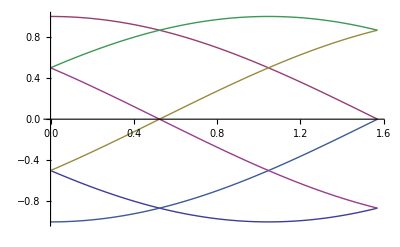

```mathematica
Plot[{1/2 (-Cos[θ]-√3 Sin[θ]),Cos[θ],1/2 (-Cos[θ]+√3 Sin[θ]),1/2 (Cos[θ]+√3 Sin[θ]),-Cos[θ],1/2 (Cos[θ]-√3 Sin[θ])},{θ,0,Pi /2}]
```

```mathematica
ACornerRanges[θ_]:= {{1/2 ( Cos[θ]-√3 Sin[θ]),1/2 (- Cos[θ]+√3 Sin[θ])},{1/2 ( Cos[θ]+√3 Sin[θ]),1/2 (- Cos[θ]-√3 Sin[θ])},{Cos[θ],-Cos[θ]}}
```

```mathematica
ACornerRanges[0]
ACornerRanges[Pi/6]
ACornerRanges[Pi/3]
ACornerRanges[Pi/2]
```

{{1/2,-1/2},{1/2,-1/2},{1,-1}}

{{0,0},{(√3)/2,-(√3)/2},{(√3)/2,-(√3)/2}}

{{-1/2,1/2},{1,-1},{1/2,-1/2}}

{{-(√3)/2,(√3)/2},{(√3)/2,-(√3)/2},{0,0}}

```mathematica
ACornerRanges[θ_]:=Piecewise[{{{Cos[θ],-Cos[θ]},θ<Pi/6 && (θ>0||θ>11Pi/6)},{{1/2 ( Cos[θ]+√3 Sin[θ]),1/2 (- Cos[θ]-√3 Sin[θ])},θ< Pi/2 && θ>Pi/6 },{{1/2 ( Cos[θ]-√3 Sin[θ]),1/2 (- Cos[θ]+√3 Sin[θ])},θ<5Pi/6 && θ>Pi/2 },{{-Cos[θ],Cos[θ]},θ<7 Pi/6 && θ>5Pi/6},{{-1/2 ( Cos[θ]+√3 Sin[θ]),1/2 ( Cos[θ]+√3 Sin[θ])},θ< 9 Pi/6 && θ>7 Pi/6 },{{-1/2 ( Cos[θ]-√3 Sin[θ]),1/2 ( Cos[θ]-√3 Sin[θ])},θ<11Pi/6 && θ>9 Pi/6 }}]
```

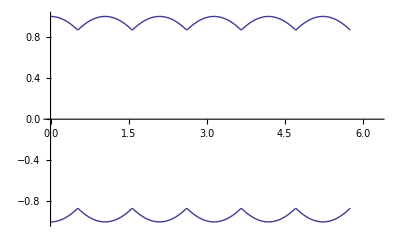

```mathematica
Plot[ACornerRanges[θ],{θ,0,2Pi }]
```

```mathematica
FCos[θ]-√3 Sin[θ]
```

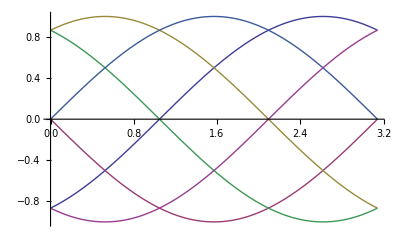

```mathematica
Plot[{1/2 (-√3 Cos[θ]+Sin[θ]),-Sin[θ],1/2 (√3 Cos[θ]+Sin[θ]),1/2 (√3 Cos[θ]-Sin[θ]),Sin[θ],1/2 (-√3 Cos[θ]-Sin[θ])},{θ,0,Pi }]
```

```mathematica
BCornerRanges[θ_]:= {{1/2 (√3 Cos[θ]-Sin[θ]),1/2 (-√3 Cos[θ]+Sin[θ])},{1/2 (√3 Cos[θ]+Sin[θ]),1/2 (-√3 Cos[θ]-Sin[θ])},{Sin[θ],-Sin[θ]}}
```

```mathematica
BCornerRanges[0]
BCornerRanges[Pi/6]
BCornerRanges[Pi/3]
BCornerRanges[Pi/2]
```

{{(√3)/2,-(√3)/2},{(√3)/2,-(√3)/2},{0,0}}

{{1/2,-1/2},{1,-1},{1/2,-1/2}}

{{0,0},{(√3)/2,-(√3)/2},{(√3)/2,-(√3)/2}}

{{-1/2,1/2},{1/2,-1/2},{1,-1}}

```mathematica
BCornerRanges[θ_]:=Piecewise[{{{1/2 (√3 Cos[θ]+Sin[θ]),1/2 (-√3 Cos[θ]-Sin[θ])},θ<Pi/3 && θ>0},{{Sin[θ],-Sin[θ]},θ<2 Pi/3 && θ>Pi/3 },{{1/2 (√3 Cos[θ]-Sin[θ]),1/2 (-√3 Cos[θ]+Sin[θ])},θ<Pi && θ>2 Pi/3 }}]
```

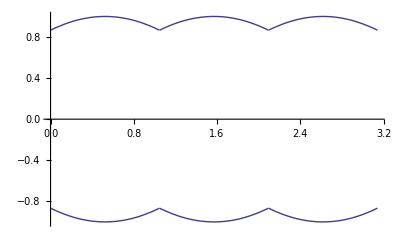

```mathematica
Plot[BCornerRanges[θ],{θ,0,Pi }]
```

```mathematica
CornerRanges[0]
```

{{0,1},{1,-1},{(√3)/2,-(√3)/2}}

```mathematica
CornerRanges[θ_]:={{0,1},{-Cos[Mod[θ-Pi/6,Pi/3]-Pi/6],Cos[Mod[θ-Pi/6,Pi/3]-Pi/6]},{-Cos[Mod[θ,Pi/3]-Pi/6],Cos[Mod[θ,Pi/3]-Pi/6]}}
```

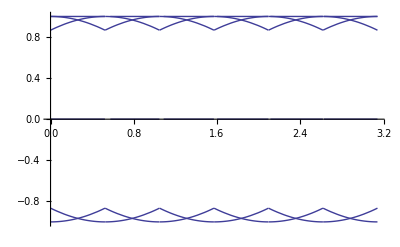

```mathematica
Plot[CornerRanges[θ],{θ,0,Pi }]
```

```mathematica
nScaleMatrix[θ_]:= {{1/Sqrt[3],0,0},{0,Sqrt[3/8]/Cos[Mod[θ-Pi/6,Pi/3]-Pi/6],0},{0,0,Sqrt[3/8]/Cos[Mod[θ,Pi/3]-Pi/6]}};
nYAB[θ_]:=FullSimplify[nScaleMatrix[θ]. RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]];
MatrixForm[nYAB[θ]]
MatrixForm[FullSimplify[nYAB[θ]]. RGBCube]
```

(1/3 | 1/3 | 1/3
-1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]) | 1/2 Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] | 1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ])
1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ]) | -1/2 Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ] | 1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]))

(0 | 1/3 | 1/3 | 1/3 | 2/3 | 2/3 | 2/3 | 1
0 | -1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]) | 1/2 Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] | 1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ]) | 1/2 Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]]+1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ]) | 1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ])-1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]) | 1/2 Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]]-1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]) | 1/2 Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]]+1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ])-1/4 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ])
0 | 1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ]) | -1/2 Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ] | 1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]) | -1/2 Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ]+1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]) | 1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ])+1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]) | -1/2 Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ]+1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ]) | -1/2 Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ]+1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ])+1/4 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]))

```mathematica
CForm[nYAB[θ]]
```

List(List(0.3333333333333333,0.3333333333333333,0.3333333333333333),
   List(-(Sec(θ - (Pi*Floor(0.5 + (3*θ)/Pi))/3.)*(Cos(θ) + Sqrt(3)*Sin(θ)))/4.,(Cos(θ)*Sec(θ - (Pi*Floor(0.5 + (3*θ)/Pi))/3.))/2.,
    (Sec(θ - (Pi*Floor(0.5 + (3*θ)/Pi))/3.)*(-Cos(θ) + Sqrt(3)*Sin(θ)))/4.),
   List((Sec((Pi - 6*(θ % Pi/3.))/6.)*(-(Sqrt(3)*Cos(θ)) + Sin(θ)))/4.,-(Sec((Pi - 6*(θ % Pi/3.))/6.)*Sin(θ))/2.,
    (Sec((Pi - 6*(θ % Pi/3.))/6.)*(Sqrt(3)*Cos(θ) + Sin(θ)))/4.))

```mathematica
MatrixForm[boxRange[FullSimplify[nYAB[θ]. RGBCube]]]
```

(0 | 1
Min[0,-Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]],Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]],1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]-√3 Sin[θ]),1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ]),-1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]),1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ])] | Max[0,-Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]],Cos[θ] Sec[θ-1/3 π Floor[1/2+(3 θ)/π]],1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]-√3 Sin[θ]),1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (-Cos[θ]+√3 Sin[θ]),-1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ]),1/2 Sec[θ-1/3 π Floor[1/2+(3 θ)/π]] (Cos[θ]+√3 Sin[θ])]
Min[0,1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]-Sin[θ]),-Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ],Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ],1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ]),-1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]),1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ])] | Max[0,1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]-Sin[θ]),-Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ],Sec[1/6 (π-6 Mod[θ,π/3])] Sin[θ],1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (-√3 Cos[θ]+Sin[θ]),-1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ]),1/2 Sec[1/6 (π-6 Mod[θ,π/3])] (√3 Cos[θ]+Sin[θ])])

```mathematica
Manipulate[Grid[{{MatrixForm[boxRange[FullSimplify[nYAB[θ]. RGBCube]]],MatrixForm[boxRange[FullSimplify[YAB[θ]. RGBCube]]],MatrixForm[CornerRanges[θ]]}}],{θ,0,Pi}]
```

Part::partw: Part 3 of YAB[2.16142] . {{0, 1, 0, 0, 0, 1, 1, 1}, {0, 0, 1, 0, 1, 0, 1, 1}, {0, 0, 0, 1, 1, 1, 0, 1}} does not exist.

```mathematica
MatrixForm[N[nYAB[Pi/12]]]
```

(0.333333 | 0.333333 | 0.333333
-0.366025 | 0.5 | -0.133975
-0.366025 | -0.133975 | 0.5)

```mathematica
MatrixForm[boxRange[YAB[0]. RGBCube]]
MatrixForm[boxRange[YAB[Pi/6]. RGBCube]]
MatrixForm[boxRange[YAB[Pi/4]. RGBCube]]
MatrixForm[boxRange[YAB[Pi/3]. RGBCube]]
MatrixForm[boxRange[YAB[Pi/2]. RGBCube]]
```

(0 | 1
-1 | 1
-(√3)/2 | (√3)/2)

(0 | 1
-(√3)/2 | (√3)/2
-1 | 1)

(0 | 1
-(√(3/2))/2-1/(2 √2) | (√(3/2))/2+1/(2 √2)
-(√(3/2))/2-1/(2 √2) | (√(3/2))/2+1/(2 √2))

(0 | 1
-1 | 1
-(√3)/2 | (√3)/2)

(0 | 1
-(√3)/2 | (√3)/2
-1 | 1)

```mathematica
N[√3]
```

1.73205

```mathematica
N[2 √2]
```

2.82843

```mathematica
boxRange[YAB[θ]. RGBCube,θ]
```

{{{0,1},{-1,1},{-1,1}},{{0,0},{π/3,(5 π)/3},{(11 π)/6,(7 π)/6}}}

```mathematica
CForm[YAB[θ]]
```

List(List(1/Sqrt(3),1/Sqrt(3),1/Sqrt(3)),List(-(Cos(θ)/Sqrt(6)) - Sin(θ)/Sqrt(2),Sqrt(0.6666666666666666)*Cos(θ),-(Cos(θ)/Sqrt(6)) + Sin(θ)/Sqrt(2)),
   List(-(Cos(θ)/Sqrt(2)) + Sin(θ)/Sqrt(6),-(Sqrt(0.6666666666666666)*Sin(θ)),Cos(θ)/Sqrt(2) + Sin(θ)/Sqrt(6)))

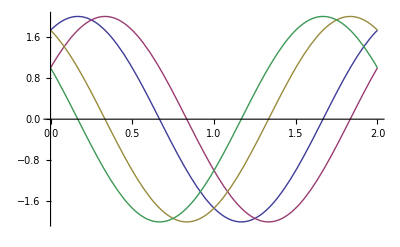

```mathematica
Plot[{√3 Cos[θ Pi]+ Sin[θ Pi],Cos[θ Pi]+√3 Sin[θ Pi],√3 Cos[θ Pi]- Sin[θ Pi],Cos[θ Pi]-√3 Sin[θ Pi]},{θ,0,2 }]
```

```mathematica
MatrixForm[RGBCube]
```

(0 | 1 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 1 | 0 | 1)

```mathematica
FullSimplify[√3 RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]]
```

{{1,1,1},{-(Cos[θ]+√3 Sin[θ])/(√2),√2 Cos[θ],(-Cos[θ]+√3 Sin[θ])/(√2)},{(-√3 Cos[θ]+Sin[θ])/(√2),-√2 Sin[θ],(√3 Cos[θ]+Sin[θ])/(√2)}}

```mathematica
FullSimplify[ArcTan[1/Sqrt[2]]/Pi]
```

ArcCot[√2]/π

```mathematica
Sin[Pi/3]
```

(√3)/2

```mathematica
RotationMatrixX[-Pi/4]. {{1/(√3)},{1/(√3)},{1/(√3)}}
RotationMatrixY[-ArcTan[Sqrt[2]]]. %
```

{{1/(√3)},{0},{√(2/3)}}

{{1},{0},{0}}

```mathematica
RotationMatrixZ[θ].RotationMatrixY[-ArcTan[Sqrt[2]]].RotationMatrixX[-Pi/4]
```

{{Cos[θ]/(√3),Cos[θ]/(√3)+Sin[θ]/(√2),Cos[θ]/(√3)-Sin[θ]/(√2)},{-Sin[θ]/(√3),Cos[θ]/(√2)-Sin[θ]/(√3),-Cos[θ]/(√2)-Sin[θ]/(√3)},{-√(2/3),1/(√6),1/(√6)}}

```mathematica
RotationMatrixX[Pi/4]. {{1/(√3)},{1/(√3)},{1/(√3)}}
RotationMatrixY[-ArcTan[1/(√2)]]. %
```

{{1/(√3)},{√(2/3)},{0}}

{{(√2)/3},{√(2/3)},{-1/3}}

```mathematica
N[ArcCos[√3]]
N[ArcSin[√3]]
```

0.+1.14622 ⅈ

1.5708-1.14622 ⅈ

```mathematica
RotationMatrixY[θ]
```

{{Cos[θ],0,-Sin[θ]},{0,1,0},{Sin[θ],0,Cos[θ]}}

```mathematica
RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]
```

{{1/(√3),1/(√3),1/(√3)},{-1/(√6),√(2/3),-1/(√6)},{-1/(√2),0,1/(√2)}}

```mathematica
RotationMatrixZ[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4]
```

{{(√(2/3) Cos[θ]-Sin[θ]/(√3))/(√2),Cos[θ]/(√3)+√(2/3) Sin[θ],(√(2/3) Cos[θ]-Sin[θ]/(√3))/(√2)},{(-Cos[θ]/(√3)-√(2/3) Sin[θ])/(√2),√(2/3) Cos[θ]-Sin[θ]/(√3),(-Cos[θ]/(√3)-√(2/3) Sin[θ])/(√2)},{-1/(√2),0,1/(√2)}}

```mathematica
RotationMatrixY[-Pi/4]
RotationMatrixZ[ArcTan[1/Sqrt[2]]].%
RotationMatrixY[θ].%
```

{{1/(√2),0,1/(√2)},{0,1,0},{-1/(√2),0,1/(√2)}}

{{1/(√3),1/(√3),1/(√3)},{-1/(√6),√(2/3),-1/(√6)},{-1/(√2),0,1/(√2)}}

{{Cos[θ]/(√3)+Sin[θ]/(√2),Cos[θ]/(√3),Cos[θ]/(√3)-Sin[θ]/(√2)},{-1/(√6),√(2/3),-1/(√6)},{-Cos[θ]/(√2)+Sin[θ]/(√3),Sin[θ]/(√3),Cos[θ]/(√2)+Sin[θ]/(√3)}}

```mathematica
{{0},{(2 √2)/3},{-1/3}}
```

```mathematica
√(2/3)/(1/(√3))
```

```mathematica
ArcTan[√2
```

```mathematica
N[ArcTan[1/Sqrt[3]]]
```

0.523599

π/2-ArcTan[1/(√2)]

```mathematica
Solve[R[α,β, γ]==A[],{α,β, γ}]
```

{}

```mathematica
{{Cos[γ], Sin[γ], 0}, {-Sin[γ], Cos[γ], 0}, {0, 0, 1}}
```

```mathematica
MatrixForm[R[α,β, γ]]
MatrixForm[A[]]
```

(Cos[β] Cos[γ] | Cos[β] Sin[γ] | -Sin[β]
Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ] | Cos[α] Cos[γ]+Sin[α] Sin[β] Sin[γ] | Cos[β] Sin[α]
Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ] | -Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[β])

(0.299 | 0.587 | 0.114
-0.168736 | -0.331264 | 1/2
1/2 | -0.418688 | -0.0813124)

```mathematica
Conditions=MapThread[(#1==#2)&,{Flatten[R[α,β, γ]],Flatten[A[1/3,1/3]]}];
MatrixForm[Conditions]
```

(Cos[β] Cos[γ]==1/3
Cos[β] Sin[γ]==1/3
-Sin[β]==1/3
Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]==-1/4
Cos[α] Cos[γ]+Sin[α] Sin[β] Sin[γ]==-1/4
Cos[β] Sin[α]==1/2
Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]==1/2
-Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ]==-1/4
Cos[α] Cos[β]==-1/4)

```mathematica
N[Reduce[-Sin[β]==1/(√3),{β}]]
```

C[1]∈Integers&&(β==-0.61548+6.28319 C[1]||β==3.75707+6.28319 C[1])

```mathematica
-0.6154797086703874/Pi
```

-0.195913

```mathematica
Conditions/. {β->-0.11424837933153527}
```

{0.993481 Cos[γ]==0.299,0.993481 Sin[γ]==0.587,True,-0.114 Cos[γ] Sin[α]-Cos[α] Sin[γ]==-0.168736,Cos[α] Cos[γ]-0.114 Sin[α] Sin[γ]==-0.331264,0.993481 Sin[α]==1/2,-0.114 Cos[α] Cos[γ]+Sin[α] Sin[γ]==1/2,-Cos[γ] Sin[α]-0.114 Cos[α] Sin[γ]==-0.418688,0.993481 Cos[α]==-0.0813124}

```mathematica
Solve[0.9934807496876826 Sin[γ]==0.587 ,γ]
Solve[0.9934807496876826 Cos[γ]==0.299,γ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{γ→0.632114}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{γ→-1.2651},{γ→1.2651}}

```mathematica
Conditions/. {β->-0.11424837933153527,γ->0.6321143732471498}
```

{False,True,True,-0.590852 Cos[α]-0.0919729 Sin[α]==-0.168736,0.80678 Cos[α]-0.0673571 Sin[α]==-0.331264,0.993481 Sin[α]==1/2,-0.0919729 Cos[α]+0.590852 Sin[α]==1/2,-0.0673571 Cos[α]-0.80678 Sin[α]==-0.418688,0.993481 Cos[α]==-0.0813124}

```mathematica
RotationMatrix[{{1,1,1}, {√3,0,0}}]
```

{{1/(√3),1/(√3),1/(√3)},{-1/(√3),1/6 (3+√3),1/6 (-3+√3)},{-1/(√3),1/6 (-3+√3),1/6 (3+√3)}}

```mathematica
MatrixForm[Map[FullSimplify[#]&,RotationMatrixX[α]. RotationMatrix[{{1,1,1}, {1,0,0}}],2]]
CForm[%]
```

(1/(√3) | 1/(√3) | 1/(√3)
-(Cos[α]+Sin[α])/(√3) | 1/6 ((3+√3) Cos[α]+(-3+√3) Sin[α]) | 1/6 ((-3+√3) Cos[α]+(3+√3) Sin[α])
(-Cos[α]+Sin[α])/(√3) | 1/6 ((-3+√3) Cos[α]-(3+√3) Sin[α]) | 1/6 ((3+√3) Cos[α]-(-3+√3) Sin[α]))

List(List(1/Sqrt(3),1/Sqrt(3),1/Sqrt(3)),List(-((Cos(α) + Sin(α))/Sqrt(3)),((3 + Sqrt(3))*Cos(α) + (-3 + Sqrt(3))*Sin(α))/6.,
    ((-3 + Sqrt(3))*Cos(α) + (3 + Sqrt(3))*Sin(α))/6.),List((-Cos(α) + Sin(α))/Sqrt(3),((-3 + Sqrt(3))*Cos(α) - (3 + Sqrt(3))*Sin(α))/6.,
    ((3 + Sqrt(3))*Cos(α) - (-3 + Sqrt(3))*Sin(α))/6.))

```mathematica
MatrixForm[A[]]
```

(0.299 | 0.587 | 0.114
-0.168736 | -0.331264 | 1/2
1/2 | -0.418688 | -0.0813124)

```mathematica
MatrixForm[A[1/3,1/3]]
```

(1/3 | 1/3 | 1/3
-1/4 | -1/4 | 1/2
1/2 | -1/4 | -1/4)